# IceCube sterile neutrino analysis data release

## Looking at the data

We can use the following function to load the data into a Mathematica array.

```mathematica
Data=Cases[Import[StringJoin[{NotebookDirectory[],"../../data/observed_events.dat"}], "Data"],{_?NumberQ,___}];
```

Each data entry has two numbers. The first number is the reconstructed muon energy and the second number the zenith angle in radians. We can use the following functions to plot the energy and cos(θ) distributions.

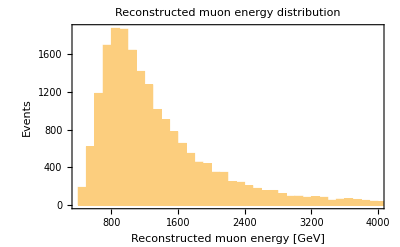

```mathematica
DataEnergyDistribution=Histogram[#⟦1⟧&/@Data,Frame->True,PlotLabel->"Reconstructed muon energy distribution",FrameLabel->{"Reconstructed muon energy [GeV]","Events"}]
```

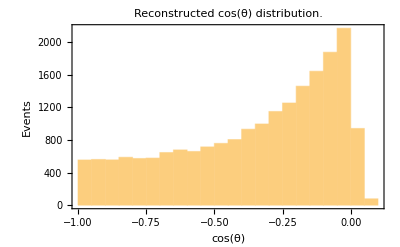

```mathematica
DataZenithDistribution=Histogram[Cos[#⟦2⟧]&/@Data,Frame->True,PlotLabel->"Reconstructed cos(θ) distribution.",FrameLabel->{"cos(θ)","Events"}]
```

## Using the nominal MC and comparing it with the data

We can use the following function to load the IceCube Monte Carlo into a Mathematica array. (Warning: since the MC is very large the commands on this section may take a couple of minutes to execute, for alternative ways to estimate the detector response look at the next section).

```mathematica
MC=Cases[Import[StringJoin[{NotebookDirectory[],"../../monte_carlo/NuFSGenMC_nominal.dat"}], "Data"],{_?NumberQ,___}];
```

To calculate the expected energy distribution we have to multiply the monte carlo event weight by the total neutrino flux. In this example we will use the provided Honda+Gaisser model with π/K ratio of 1.1; see the README and the paper for more details.

```mathematica
PIKR=1.1;(* relative pion to kaon contributions*)
MCWeight=#⟦6⟧*(#⟦7⟧+PIKR*#⟦8⟧)&/@MC;
```

```mathematica
MCEventsRecoEnergy=#⟦2⟧&/@MC;
```

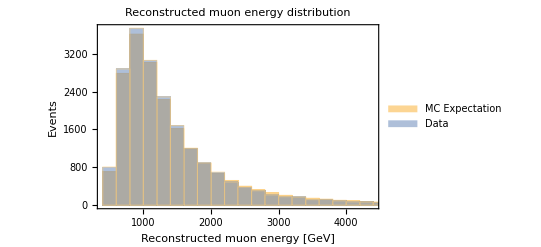

```mathematica
Histogram[{WeightedData[MCEventsRecoEnergy,MCWeight],#⟦1⟧&/@Data},ChartLegends->Placed[{"MC Expectation","Data"},Above],Frame->True,PlotLabel->"Reconstructed muon energy distribution",FrameLabel->{"Reconstructed muon energy [GeV]","Events"}]
```

```mathematica
MCEventsCosTh=#⟦3⟧&/@MC;
```

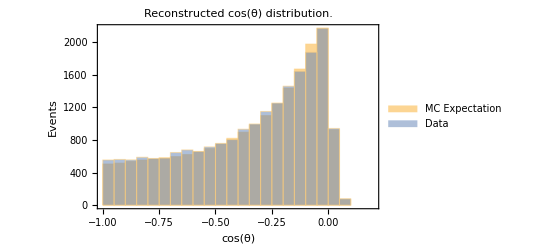

```mathematica
Histogram[{WeightedData[MCEventsCosTh,MCWeight],Cos[#⟦2⟧]&/@Data},ChartLegends->Placed[{"MC Expectation","Data"},Above],Frame->True,PlotLabel->"Reconstructed cos(θ) distribution.",FrameLabel->{"cos(θ)","Events"},PlotRange->{{-1,0.2},Automatic}]
```

## Using the detector response arrays

Besides the nominal MC we further provide the detector response arrays for the nominal configuration and also for systematic detector configurations, e.g. different ice models, change of D.O.M. efficiency.

In this example we will first use the nominal response array to construct the energy and zenith distribution, and then we will repeat for the D.O.M. efficiency variants.

Loading the detector response array

The following command allows us to know the HDF5 file content

```mathematica
Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_nominal_response_array.h5"}]]
```

{/antineutrino_response_array,/costh_bin_edges,/neutrino_response_array,/proxy_energy_bin_edges,/true_energy_bin_edges}

Get the bin edges

```mathematica
CosThBinEdges=Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_nominal_response_array.h5"}],{"Datasets","/costh_bin_edges"}];
ProxyEnergyBinEdges=Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_nominal_response_array.h5"}],{"Datasets","/proxy_energy_bin_edges"}];
```

Get the response arrays

```mathematica
NominalNeutrinoResponseArray=Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_nominal_response_array.h5"}],{"Datasets","/neutrino_response_array"}];
NominalAntineutrinoResponseArray=Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_nominal_response_array.h5"}],{"Datasets","/antineutrino_response_array"}];
```

Loading the averaged atmospheric neutrino flux

In order to estimate the number of events we need to convolute the response arrays with the averaged neutrino/antineutrino flux per bin. We can use the provided Honda+Gaisser averaged neutrino flux in the same binning, which has the following properties

```mathematica
Import[StringJoin[{NotebookDirectory[],"../../atmospheric_flux/averaged/HondaGaisser.h5"}]]
```

{/average_flux_nu_kaon,/average_flux_nu_pion,/average_flux_nubar_kaon,/average_flux_nubar_pion,/costh_reco_bin_edges,/e_true_bin_edges}

it has been constructed such that the bin edges match the response arrays edges, so we can readily convolute them.

```mathematica
PIKR=1.1;
```

```mathematica
NeutrinoKaonFlux=Import[StringJoin[{NotebookDirectory[],"../../atmospheric_flux/averaged/HondaGaisser.h5"}],{"Datasets","/average_flux_nu_kaon"}];
NeutrinoPionFlux=Import[StringJoin[{NotebookDirectory[],"../../atmospheric_flux/averaged/HondaGaisser.h5"}],{"Datasets","/average_flux_nu_pion"}];
NeutrinoFlux=NeutrinoPionFlux+PIKR*NeutrinoKaonFlux;
```

```mathematica
AntineutrinoKaonFlux=Import[StringJoin[{NotebookDirectory[],"../../atmospheric_flux/averaged/HondaGaisser.h5"}],{"Datasets","/average_flux_nubar_kaon"}];
AntineutrinoPionFlux=Import[StringJoin[{NotebookDirectory[],"../../atmospheric_flux/averaged/HondaGaisser.h5"}],{"Datasets","/average_flux_nubar_pion"}];
AntineutrinoFlux=AntineutrinoPionFlux+PIKR*AntineutrinoKaonFlux;
```

Convolution of the response array with the atmospheric flux

We can calculate the event expectation in each reconstructed energy and cos(θ) bin using the following simple expression

```mathematica
EventExpectation=(MapThread[Dot,{#,NeutrinoFlux}]&/@NominalNeutrinoResponseArray)+(MapThread[Dot,{#,AntineutrinoFlux}]&/@NominalAntineutrinoResponseArray);
```

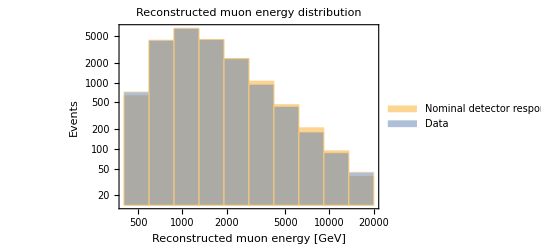

```mathematica
Histogram[{WeightedData[Total[#]/2&/@Partition[ProxyEnergyBinEdges,2,1],Total/@EventExpectation],#⟦1⟧&/@Data},{"Log",{ProxyEnergyBinEdges}},"LogCount",ChartLegends->Placed[{"Nominal detector response","Data"},Above],Frame->True,PlotLabel->"Reconstructed muon energy distribution",FrameLabel->{"Reconstructed muon energy [GeV]","Events"}]
```

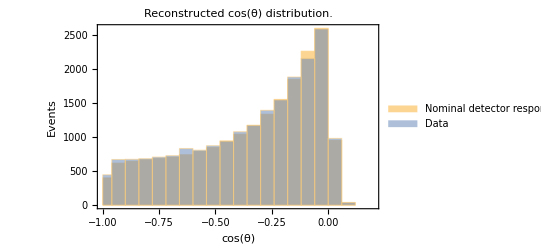

```mathematica
Histogram[{WeightedData[Total[#]/2&/@Partition[CosThBinEdges,2,1],Total/@Transpose[EventExpectation]],Cos[#⟦2⟧]&/@Data},{CosThBinEdges},ChartLegends->Placed[{"Nominal detector response","Data"},Above],Frame->True,PlotLabel->"Reconstructed cos(θ) distribution.",FrameLabel->{"cos(θ)","Events"},PlotRange->{{-1,0.2},Automatic}]
```

Example of systematic response arrays: DOM effiency changes

First lets load the different DOM efficiency response arrays.

```mathematica
DOMEffVariantsLabels={"0_90","1_1979"};
```

```mathematica
DOMEffVariantsNeutrinoResponseArray=Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_dom_eff_"<>#<>"_response_array.h5"}],{"Datasets","/neutrino_response_array"}]&/@DOMEffVariantsLabels;
DOMEffVariantsAntiNeutrinoResponseArray=Import[StringJoin[{NotebookDirectory[],"../../systematics_response_arrays/nufsgen_dom_eff_"<>#<>"_response_array.h5"}],{"Datasets","/antineutrino_response_array"}]&/@DOMEffVariantsLabels;
```

Then we do the convolution

```mathematica
EventExpectationVariants=Map[MapThread[Dot,{#,NeutrinoFlux}]&,DOMEffVariantsNeutrinoResponseArray,{2}]+Map[MapThread[Dot,{#,AntineutrinoFlux}]&,DOMEffVariantsAntiNeutrinoResponseArray,{2}];
```

We plot the resulting reconstructed muon energy distribution

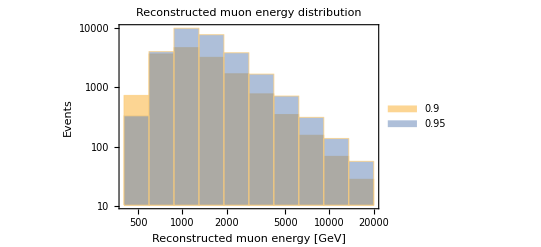

```mathematica
Histogram[Function[u,WeightedData[Total[#]/2&/@Partition[ProxyEnergyBinEdges,2,1],Total/@u]]/@EventExpectationVariants,
{"Log",{ProxyEnergyBinEdges}},"LogCount",
ChartLegends->Placed[{"0.9","0.95","1.089","1.1979"},Above],Frame->True,PlotLabel->"Reconstructed muon energy distribution",FrameLabel->{"Reconstructed muon energy [GeV]","Events"}]
```